```mathematica
Equals


g[x_]  = x + 9
x = 5
g[10]
```

```mathematica
g1[x_]  := x + 9
g1[10]
```

```mathematica
y:= Random[]
y+2
```

```mathematica
2==3
```

False

```mathematica
3!=4
```

True

```mathematica
f=#^2& 
f[x]
```

#1^2&

```mathematica
(* test comment *)
```

16

```mathematica
2(a+1) ==2a + 2
```

True

```mathematica
abs[x_]:= If[x>= 0, x, -x]
```

```mathematica
abs/@{-1,0,1}
```

```mathematica
{1,0,1}
a={1, 2, 3, 4}
a[[1]]
```

{1,0,1}

{1,2,3,4}

1

```mathematica
Take[a, -1]
```

{4}

```mathematica
{1, 2, 3, 4} + {1, 2, 2, 3}
```

{2,4,5,7}

```mathematica
a * a 
a^(a+1)
```

{1,4,9,16}

{1,8,81,1024}

```mathematica
a.a
join[a, a]
```

30

join[{1,2,3,4},{1,2,3,4}]

```mathematica
x = .
```

```mathematica
x/(x+1) /. x -> 4
```

```mathematica
4/5
 1+ x + x^2 /. {x + 1 -> 1}
1+ x + y*x^2 //. {x + 1 -> 1, y-> x^2}
```

4/5

1+x^2

1+0.53236 x^2

```mathematica
Cases[{x^2, x^3, x^4, x^5, {a, b}^2, (x+y)^2}, a_^(b_?EvenQ)]
```

{x^2,x^4}

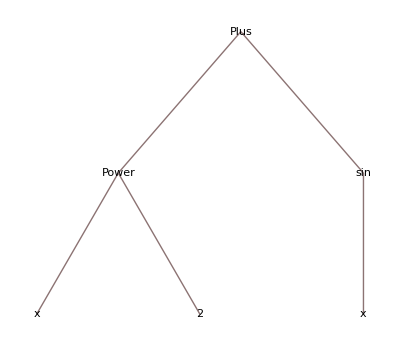

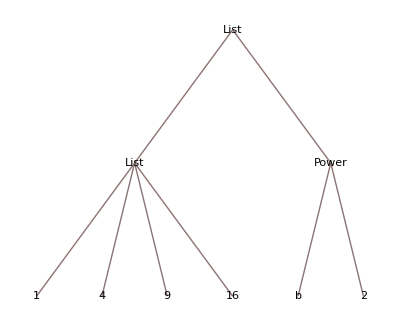

```mathematica
{x^2,x^4}

x^2 + sin[x]//TreeForm

{a, b}^2 //TreeForm
```

```mathematica
y=.
```

```mathematica
a= Sqrt[x]/Sqrt[y]
```

(√x)/(√y)

```mathematica
a//Treeform
```

Treeform[(√x)/(√y)]

```mathematica
a/. {Sqrt[x] -> b, Sqrt[y] -> c}
```

```mathematica
b/(√y)
```

b/(√y)